```mathematica
(*Tripple Dot*)
```

```mathematica
(*Spin Matrices*)
σ0=({{1, 0}, {0, 1}});
σx=({{0, 1}, {1, 0}});
σy=({{0, ⅈ}, {-ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*Majorana operators*)
γx1d=KroneckerProduct[σx,σ0,σ0,σ0,σ0,σ0];
γx1u=KroneckerProduct[σz,σx,σ0,σ0,σ0,σ0];
γx2d=KroneckerProduct[σz,σz,σx,σ0,σ0,σ0];
γx2u=KroneckerProduct[σz,σz,σz,σx,σ0,σ0];
γx3d=KroneckerProduct[σz,σz,σz,σz,σx,σ0];
γx3u=KroneckerProduct[σz,σz,σz,σz,σz,σx];

γy1d=KroneckerProduct[σy,σ0,σ0,σ0,σ0,σ0];
γy1u=KroneckerProduct[σz,σy,σ0,σ0,σ0,σ0];
γy2d=KroneckerProduct[σz,σz,σy,σ0,σ0,σ0];
γy2u=KroneckerProduct[σz,σz,σz,σy,σ0,σ0];
γy3d=KroneckerProduct[σz,σz,σz,σz,σy,σ0];
γy3u=KroneckerProduct[σz,σz,σz,σz,σz,σy];

γx={γx1u,γx1d,γx2u,γx2d,γx3u,γx3d};
γy={γy1u,γy1d,γy2u,γy2d,γy3u,γy3d};

(*Dirac operators*)
dd=Table[1/2(γx[[i]]+ⅈ γy[[i]]),{i,1,6}];
d=Table[1/2(γx[[i]]-ⅈ γy[[i]]),{i,1,6}];
```

```mathematica
(*Parameters*)
α=0.08*0;  (*Spin Orbit Coupling*)
ϵ=Table[0.0,{i,1,6}];  
Δ=0.5;  (*Induced Superconducing Gap*)
B=0.0;  (*Magnetic Feild *)
t=-0.1;  (*Hopping*)
U=1.0;  (*Electron-Electron interaction*)
ev=0.05; (*Voltage*)
Eϵ=Table[{},{n,1,2^6}];
ϵ2=0.2; (*Potential for Dot Two*)
ϵ3=0.9; (*Potential for Dot Three*)
For[ϵ1=-1.0,ϵ1≤1.0,ϵ1+=0.1,
For[ϵ2=-1.0,ϵ2≤1.0,ϵ2+=0.1,

ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+t Sum[dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]],{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+Δ Sum[dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]],{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];

For[n=1,n≤2^6,n++,
Eϵ[[n]]=Join[Eϵ[[n]],{{ϵ1,ϵ2,e[[n]]-e[[1]]}}];
];
];
Print[ϵ1];
];
```

-1.

-0.9

-0.8

-0.7

-0.6

-0.5

-0.4

-0.3

-0.2

-0.1

-1.38778×10^-16

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

```mathematica
ListPlot3D[{Eϵ[[1]],Eϵ[[2]],Eϵ[[3]]}]
```

-Graphics3D-

```mathematica
e2=Table[0,{i,1,Length[Eϵ[[2]]]}];
For[i=1,i≤Length[Eϵ[[2]]],i++,
If[Eϵ[[2,i,3]]>0.001,
e2[[i]]=Eϵ[[2,i]],
e2[[i]]=Eϵ[[3,i]],
];
];
```

```mathematica
bounds=Table[{e2[[i,1]],e2[[i,2]],0},{i,1,Length[Eϵ[[2]]]}];
tst=Table[{e2[[i,1]],e2[[i,2]],0},{i,1,Length[Eϵ[[2]]]}];
For[i=1,i≤Length[Eϵ[[2]]],i++,
tst[[i,3]]=Abs[Eϵ[[2,i,3]]-Eϵ[[1,i,3]]];
If[Abs[e2[[i,3]]-Eϵ[[1,i,3]]]<0.1,
bounds[[i,3]]=1];
];
```

```mathematica
pty[ϵ1_,ϵ2_]:=Block[{ptp},
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+t Sum[dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]],{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+Δ Sum[dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]],{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];
(*Parity*)
n=1;
p=Table[-ⅈ Conjugate[Ψ[[n]]].γy[[i]].γx[[i]].Ψ[[n]],{i,1,6}];
no=Table[Conjugate[Ψ[[n]]].dd[[i]].d[[i]].Ψ[[n]],{i,1,6}];ptp={Round[no[[1]]+no[[2]],0.1],Round[no[[3]]+no[[4]],0.1],Round[no[[5]]+no[[6]],0.1]};

ptp
];
```

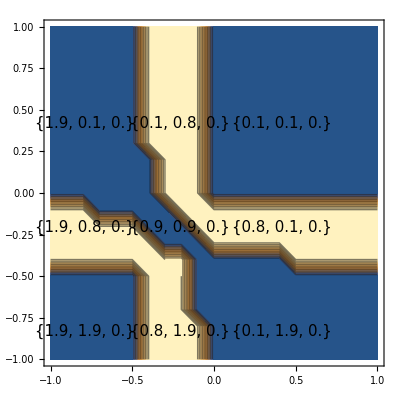

```mathematica
cm=ListContourPlot[bounds,Epilog->{{Text[Style[ToString[pty[-0.9,-0.9]],15],Scaled[{0.12,0.1}]]},{Text[Style[ToString[pty[-0.2,-0.9]],15],Scaled[{0.4,0.1}]]},{Text[Style[ToString[pty[0.5,-0.9]],15],Scaled[{0.7,0.1}]]},{Text[Style[ToString[pty[-0.9,-0.2]],15],Scaled[{0.12,0.4}]]},{Text[Style[ToString[pty[-0.9,0.5]],15],Scaled[{0.12,0.7}]]},{Text[Style[ToString[pty[-0.2,-0.2]],15],Scaled[{0.4,0.4}]]},{Text[Style[ToString[pty[-0.2,0.5]],15],Scaled[{0.7,0.4}]]},{Text[Style[ToString[pty[0.5,-0.2]],15],Scaled[{0.4,0.7}]]},{Text[Style[ToString[pty[0.5,0.5]],15],Scaled[{0.7,0.7}]]}}]
```